# Cuaderno de prácticas de Álgebra

## Práctica 4

Nombre:
Apellidos:
DNI: 77435547K
Fecha de nacimiento:
Grupo de teoría:
Grupo de prácticas:

## Ejercicio 1.

Sea W el conjunto formado por todas las cifras distintas que componen su DNI junto con todas las letras distintas de su primer apellido. 

Consideramos el grafo no orientado G1 cuyo conjunto de vértices es W y donde dos vértices cuañesquiera serán adyacentes si y sólo si son:
	i) Un número par y una vocal.
	ii) Un número impar y una consonante.
	iii) Dos números pares distintos.
	
Consideramos el grafo dirigido G2 cuyo conjunto de vértices es W y donde el conjunto de flechas está formado por todas aquellas flechas que podemos considerar de la forma:
	i) Origen en un número impar y fin de una vocal
	ii) Origen en una vocal y fin en una consonante.
	iii) Origen en un número par y fin en un número impar.
	
Se pide:

### I) Definir G1 y G2 directamente por sus conjuntos de vértices y lados o flechas.

```mathematica
W = {7, 4, 3, 5, c, a, m, h, o};

G1 = {{4, a}, {4, o},{3, c},{3, m},{3, h},{5, c},{5, m},{5, h},{7, c},{7, m},{7, h}};

G2 = {3 -> a,3 -> o,5 ->  a,5 ->  o, 7 ->  a, 7 ->  o, a ->  c,a ->  m,a ->  h,o ->  c,o ->  m,o ->  h,4 ->  3,4 ->  5,4 -> 7};
```

### II) Calcular las matrices de adyacencia de G1 y G2.

```mathematica
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
```

```mathematica
matriz1 = MATRIZADYACENCIA[W, G1];  
MatrixForm[matriz1]
```

(0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
matriz2 = MATRIZADYACENCIADIR[W, G2] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)

### III) Calcular la matriz de incidencia de G1.

```mathematica
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

```mathematica
MATRIZINCIDENCIA[W, G1] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### IV) Representar gráficamente G1 y G2.

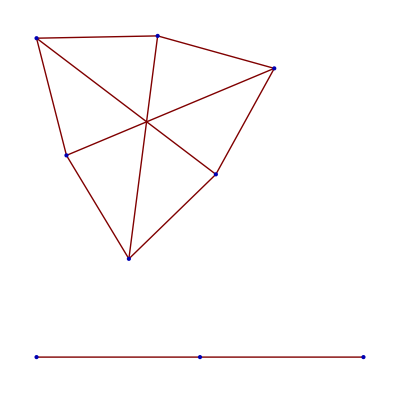

```mathematica
GraphPlot[matriz1]
```

```mathematica
GraphPlot[matriz2]
```

GraphPlot::grph: (0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0) is not a valid graph.

GraphPlot[(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0)]

## Ejercicio 2

Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

### Grafo a)

```mathematica
W1 = {1, 2, 3, 4, 5, 6};
F1 = {1 -> 2, 3 -> 1, 4 -> 5, 6 -> 1};
```

```mathematica
matrizad1 = MATRIZADYACENCIA[W1, F1] // MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

```mathematica
MATRIZINCIDENCIA[W1,F1] // MatrixForm
```

(1 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
GraphPlot[matrizad1,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

GraphPlot::grph: (0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0) is not a valid graph.

GraphPlot[(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0),EdgeRenderingFunction→({Arrow[#1,0.1]}&)]

### Grafo b)

```mathematica
matrizad2 = MatrixForm[{{0, 1, 0,1}, {1,0,1,0},{0,1,0,1},{1,0,1,0}}]
```

(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0)

```mathematica
W2 = {1, 2,3 ,4};
F2 = {1 -> 2, 1->4, 2->3, 3->4};
```

```mathematica
MATRIZINCIDENCIA[W2, F2] // MatrixForm
```

(1 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1)

```mathematica
GraphPlot[matrizad2,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

GraphPlot::grph: (0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0) is not a valid graph.

GraphPlot[(0 | 1 | 0 | 1
1 | 0 | 1 | 0
0 | 1 | 0 | 1
1 | 0 | 1 | 0),EdgeRenderingFunction→({Arrow[#1,0.1]}&)]

### Grafo c)

```mathematica
matrizincidencia={{1, 1,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,1,0,1,0},{0,1,0,1,0,1}};

W=Table[i,{i,Dimensions[matrizincidencia][[1]]}]
F={};
Do[
    AppendTo[F,Position[Transpose[matrizincidencia][[i]],1][[1]][[1]]->Position[Transpose[matrizincidencia][[i]],1][[2]][[1]]]
    ,{i,Dimensions[matrizincidencia][[2]]}];
F
```

```mathematica
W3 ={1,2,3,4,5};
```

```mathematica
F3 = {1->4,1->5,2->4,2->5,3->4,3->5};
```

```mathematica
matrizad3 = MATRIZADYACENCIA[W3, F3] // MatrixForm
```

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

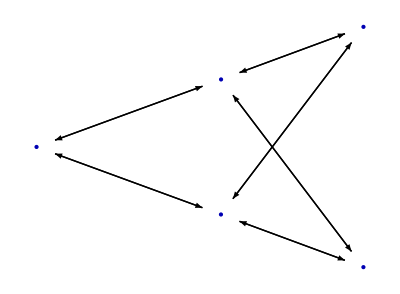

```mathematica
GraphPlot[matrizad3,EdgeRenderingFunction->({Arrow[#1,0.1]}&)]
```

### Grafo d.1)

### Grafo d .2)

## Ejercicio 3

Estudiar cuáles de los grafos del ejercicio 6.8 son regulares y/o completos.

### Grafo a)

```mathematica
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
```

```mathematica
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

```mathematica
REGULAR[matrizad1]
```

True

```mathematica
COMPLETO[matrizadyacencia]
```

False

### Grafo b)

```mathematica
REGULAR[matrizad2]
```

True

```mathematica
COMPLETO[matrizad2]
```

False

### Grafo c)

```mathematica
matrizincidencia={{1, 1,0,0,0,0},{0,0,1,1,0,0},{0,0,0,0,1,1},{1,0,1,0,1,0},{0,1,0,1,0,1}};
W=Table[i,{i,Dimensions[matrizincidencia][[1]]}]
F={};
Do[
    AppendTo[F,Position[Transpose[matrizincidencia][[i]],1][[1]][[1]]->Position[Transpose[matrizincidencia][[i]],1][[2]][[1]]]
    ,{i,Dimensions[matrizincidencia][[2]]}];
F
```

{1,2,3,4,5}

{1→4,1→5,2→4,2→5,3→4,3→5}

```mathematica
W3 = {1,2,3,4,5};
```

```mathematica
F3 = {1->4,1->5,2->4,2->5,3->4,3->5};
```

```mathematica
matrizad3 = MATRIZADYACENCIA[W3, F3];
```

```mathematica
REGULAR[matrizad3]
```

False

```mathematica
COMPLETO[matrizad3]
```

False

### Grafo d.1)

### Grafo d.2)